# Results from “Dynamics of a SIR epidemic model with limited medical resources, revisited again”

This Mathematica Notebook is a supplemntary material to the paper “Dynamics of a SIR epidemic model with limited medical
resources, revisited again”. It contains some of the calculations and illustrations appearing in the paper .

## I)SIR with B(s,i)=β s /(1+μ i) and T(i)=η w i/(i+w) preliminaries. Output: R0

```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,Directory];
Clear["Global`*"];
<<"def.m";(*trG*)
Params={Λ,δ,γ,β,ξ,μ,ω,α};Paramsp={Λ,δ,γ,β,ξ,μ,ω,α,η};X={s,i};
cet0={η->0};cetaBp={η->(β Λ+(γ+μ) (μ-ω Subscript[v, 1])+2 √(β Λ (γ+μ) (μ-ω Subscript[v, 1])))/(ω Subscript[v, 1])};
cetaBm={η->(β Λ+(γ+μ) (μ-ω Subscript[v, 1])-2 √(β Λ (γ+μ) (μ-ω Subscript[v, 1])))/(ω Subscript[v, 1])};cdel={δ->0};

Lgn=(γ+Λ+δ); cir={ir->γ-is};
sd=Λ/μ;R1=β/Subscript[V, 2];R0=sd R1 ;(*basic reproduction number*)
η0=sd β-Subscript[v, 2] ;ωH=(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ));

(*Conditions de positivité*)
cp=Thread[Paramsp>0];
(*conditions for switching between the parameters and particular cases*)
cv2={Subscript[v, 2]->(μ+γ+δ)};cv1={Subscript[v, 1]->(β+ μ ξ)};cV2={Subscript[V, 2]->Subscript[v, 2]+η,Subscript[v, 2]->(μ+γ+δ)};
cv={ξ ->(Subscript[v, 1]-β)/μ,δ ->Subscript[v, 2]-(μ+γ),η->Subscript[V, 2]-Subscript[v, 2]};ceta={η->α/ω};calv1={α-> ω (Subscript[v, 1]-β)/μ};
Print["R0  =",R0//.cV2," ,η0=",η0 ," ,ωH=",ωH," and critical β is ", b0=β/.Solve[R0==1,β][[1]]//FullSimplify]


(*Numerical conditions used in first tests*)
Param=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{16,2/10,12/100,1/100,1/1000,12/100,μ+γ+δ,β+ μ ξ,μ+γ+δ+η}];
(*Save["def.m",Param];*)
ParamF=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{16,2/10,12/100,1/100,1/1000,1/10,μ+γ+δ,β+ μ ξ,μ+γ+δ+η}];
paramGc=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1],Subscript[V, 2]}->{1/2,2/10,1/10,2/10,7/100,1/10,(μ+γ+δ),(β+ μ ξ),μ+γ+δ+η}];(*Parameters of Figure 4 in Zhou Fan*)
ParNumCheck=Thread[{ω,α,η}->{7/64,179/64,α/ω}];
Print["test cNN="]
cNN=Join[ParNumCheck,Param]
```

R0  =(β Λ)/(μ (γ+δ+η+μ)) ,η0=(β Λ)/μ-v_2 ,ωH=(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ)) and critical β is (μ V_2)/Λ

test cNN=

{ω→7/64,α→179/64,η→α/ω,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ}

### 0) Model, eqF, sol, Jacobian, jacE0, equation for endemic i, ie ,se2,detE2. Outputs: trE2, Discriminant

```mathematica
(*SIR  epidemic model of Fan:*) 
s1=Λ -   β s  i/(1+ξ i)-s μ ;(*λ s (1-s/K)*)
ifac=β s   /(1+ξ i)-Subscript[v, 2]  -η ω /(i+ω);
i1= i ifac;
r1=η  ω i/(i+ω)-μ r + γ i ;

dyn={s1,i1,r1}//.cv2;(*field*)
vars={s,i,r};
equi=Solve[Thread[dyn==0],vars];

 Print["( s'
i'
r')= ",dyn//MatrixForm]
 
(*Diff.sys and Numerical test:*)
varst=Through[vars[t]];(*Map[#[t]&, vars];Revarst = Thread[vars->varst]*);
diff= D[varst,t] − (dyn/.Thread[vars->varst]);
diffN=diff//.cNN;
initcond = (varst/.t->0)-{1.5, 0.5, 0.1};
eqs=Thread[Flatten[{diffN, initcond}] == 0];
ndesoln = NDSolveValue[eqs,varst,{t, 0, 1000}];
Print["simulation test when sd=",Λ/μ//.cNN]
Chop[ndesoln/.t->1000]

(*Two dimensional Fan:*)
dyn2={s1,i1}/.cv2;(*we may reduce to this dyntem since these two equations
 do not depend on r*)
 Print["For 2-dim case, ωe have ( s'
i')=",dyn2//MatrixForm]
 eqF=Thread[Flatten[dyn2==0]];
 equi2=Solve[eqF,{s,i}];
 Print[" fixed points are"]
equi2//.cNN//N
 dyn2E={s1,Simplify[i1/i]}/.cv2;
 
(*Computation of the Jacobian, Trace, Det  *)

jac=Grad[dyn2,{s,i}]//FullSimplify;
det=Det[jac]//FullSimplify;
Print["2 dim jac=",jac//MatrixForm]
jacE0=(jac/.i->0/.s->sd)//FullSimplify;
Print["jac(DFE)=", jacE0//MatrixForm]
tr=Tr[jac];
Print[" detG is"]
Timing[detG=GroebnerBasis[{s1,ifac,det},Params,X][[1]]//FullSimplify]
(*Timing[trG=GroebnerBasis[{s1,ifac,tr},Params,X][[1]]](*32 secs, long*)(*Do not simplify*)
Save["def.m",trG]*)

detE0=Det[jacE0]//FullSimplify;trE0=Tr[jacE0]//FullSimplify;

Print["Det(J(E0)=",detE0, ", and Tr(J(E0))=", Apart[trE0]]

(*Elimination of s via plugging, for trace and det*)
Print["s formula cs from first and sec eqs are"]
cs=Flatten[Solve[dyn2[[1]]==0,s]]
cs2=Flatten[Solve[(dyn2[[2]]/i)==0,s]]
se02=s/.cs2;
(*detEn=det/.s->se02 /.i->ic0;*)

deti=(det/.cs2)//.cv//Factor;
Print[" det after elim of s=", deti]
nudet=Factor[Numerator[deti]];

(*det1=(det/.cs)//FullSimplify*)
(*Print["Det i"]
deti=Simplify[(detF/.cs)( 1+ξ i)(( ω + i)^2)( μ+(μ ξ+β) i)]/.cv//FullSimplify
Print["PolynomialRemainder detR"]
detR=PolynomialRemainder[deti,poli,i];
Timing[icd=i/.Solve[detR==0,i][[1]]//FullSimplify]*)

(*Factor[Numerator[deti]]*)
Print["tr= ",tr]
tri=Together[(tr/.cs2)]//Factor;
(*trs=Together[(tr/.cs)]//Factor;*)
Print[" tr after elim of s is ", tri]
Print[" numer is nutr="]
nutr=Factor[Numerator[tri]]

(*Equation for endemic i *)
poli=Collect[Factor[Numerator[Together[dyn[[2]]/.cs]]]/(-i),i];
Print["sec. order A i^2 + B i + C=0 for endemic i is"]
polv= Collect[ poli/.cv//FullSimplify,i]
(*Mathematica Eliminate*)
el=Eliminate[eqF,{s}];
poliF=Collect[Numerator[Factor[el[[1,1]]-el[[1,2]]]/(-i)]//FullSimplify,i];
Print["check  poli/poliF="]
poli/poliF//FullSimplify

Print["coeffs are"]
cf=CoefficientList[poli,i];
Aa=cf[[3]];Bb=cf[[2]]; Cc=cf[[1]];
Print["{A,B,C} =",{Aa,Bb,Cc}//FullSimplify//.cv2]

Print["dis "]
dis=Discriminant[poli,i];


Print[" H  has coords "]
{η0,ωH}
(*Print["  and trH="]
Timing[trH=trE2/.{η->η0,ω->ωH}//.cv2//FullSimplify]*)
Print["The discriminant Δ = B^2 - 4 A C at H  is"]
(dis/.{η->η0,ω->ωH})//.cv2//FullSimplify

ie=i/.Solve[poli==0,i];ic0=(-Bb/(2 Aa));

trE2=tri/.i->ie[[2]];
trE1=tri/.i->ie[[1]];
(*Save["def.m",dis];Save["def.m",trE2]*)
se1=Λ ( 1+ξ ie[[1]])/(μ+ ie[[1]] Subscript[v, 1])(*endemic s*);
se2=Λ ( 1+ξ ie[[2]])/(μ+ ie[[2]] Subscript[v, 1]);
se0=Λ ( 1+ξ ic0)/(μ+ ic0 Subscript[v, 1]);


detE2=deti/.i->ie[[2]];
detE1=deti/.i->ie[[1]];
detE=deti /.i->ic0(* det ωhen $i=-B/(2A)**);


(*Print["i1,  icd, i2"] 
Chop[{ie[[1]],icd,ie[[2]]}//.cNN//N]*)
rest=Resultant[poli,nutr,i];
Print["similified restr"]
Timing[rests=FullSimplify[μ^2 rest//.cv]](*quicker than trG*)
Length[rests]
rest3=ω^3 Subscript[v, 1]^4 (μ Subscript[v, 2]-(μ+Subscript[v, 2]) Subscript[V, 2]) (-β Λ μ-β Λ Subscript[V, 2]+μ Subscript[V, 2]^2)+
β Subscript[v, 2] (β^3 Λ^3 (μ+β ω)+β Λ μ (-β Λ μ+μ^3-β^2 Λ ω) Subscript[V, 2]+μ^3 Subscript[v, 2]^2 (β Λ+μ^2-μ Subscript[V, 2])-
μ Subscript[v, 2] (β Λ (2 β Λ μ+μ^3+2 β^2 Λ ω)+μ Subscript[V, 2] 
(-2 β Λ μ+μ^3-3 β^2 Λ ω+β μ ω Subscript[V, 2])))+Subscript[v, 1] (-μ^2 (μ+2 β ω) Subscript[v, 2]^3 (β Λ+μ^2-μ Subscript[V, 2])+
β Λ μ (-β^2 Λ^2 (μ+β ω)+μ (β Λ μ-μ^3+β^2 Λ ω) Subscript[V, 2])+
β Subscript[v, 2] (Λ (β Λ μ^3+μ^5-2 β^3 Λ^2 ω+β^2 Λ μ (-Λ+μ ω))+Λ (-2 μ^4-2 β^3 Λ ω^2+β μ^2 (Λ-5 μ ω)) Subscript[V, 2]
+μ ω (2 β Λ μ+μ^3+2 β^2 Λ ω) Subscript[V, 2]^2)+
Subscript[v, 2]^2 (β Λ (μ^4+8 β^2 Λ μ ω+4 β^3 Λ ω^2+2 β μ^2 (Λ+2 μ ω))+μ Subscript[V, 2] 
(μ^4-10 β^2 Λ μ ω-6 β^3 Λ ω^2+β μ^2 (-2 Λ+μ ω)+2 β μ ω (μ+β ω) Subscript[V, 2])))
+ω Subscript[v, 1]^2 (β^3 Λ^3 μ+μ^2 Subscript[v, 2]^3 (β Λ+μ^2-μ Subscript[V, 2])+β Λ μ Subscript[V, 2] (β Λ μ+3 μ^3+2 β^2 Λ ω-2 μ (μ+β ω) Subscript[V, 2])
+Subscript[v, 2]^2 (-β Λ (5 μ^3+8 β^2 Λ ω+6 β μ (Λ+μ ω))+
μ Subscript[V, 2] (8 β Λ μ+μ^3+3 β (4 β Λ+μ^2) ω-2 μ (μ+2 β ω) Subscript[V, 2]))+Subscript[v, 2] (β Λ (-5 β Λ μ^2-3 μ^4+β^2 Λ (Λ-4 μ ω))+
Subscript[V, 2] (β Λ (10 μ^3+4 β^2 Λ ω+β μ (Λ+10 μ ω))+Subscript[V, 2] (-2 μ^2 (β Λ+μ^2)-3 β μ (β Λ+μ^2) 
ω+β^3 Λ ω^2-β μ ω (μ+β ω) Subscript[V, 2]))))+ω^2 Subscript[v, 1]^3 (2 Subscript[v, 2]^2 (2 β Λ-μ Subscript[V, 2]) (β Λ+μ^2-μ Subscript[V, 2])
+μ Subscript[V, 2] (-β Λ (2 β Λ+3 μ^2)+β Λ (μ-β ω) Subscript[V, 2]+μ (μ+β ω) Subscript[V, 2]^2)+
Subscript[v, 2] (β Λ μ (4 β Λ+3 μ^2)+Subscript[V, 2] (-2 β Λ (β Λ+4 μ^2)+
Subscript[V, 2] (β Λ μ+μ^3-β (2 β Λ+μ^2) ω+μ (μ+2 β ω) Subscript[V, 2]))));
resd=Resultant[poli,nudet,i];

Print["HP"]
HP=Solve[Join[{η==η0&&Bb==0},cp,{η==α/ω}]//.Param,{ω,α,η}];
HP//N
```

( s'
i'
r')= (Λ-s μ-(i s β)/(1+i ξ)
i (-γ-δ-μ+(s β)/(1+i ξ)-(η ω)/(i+ω))
i γ-r μ+(i η ω)/(i+ω))

simulation test when sd=400/3

{133.333,0,0}

For 2-dim case, ωe have ( s'
i')=(Λ-s μ-(i s β)/(1+i ξ)
i (-γ-δ-μ+(s β)/(1+i ξ)-(η ω)/(i+ω)))

fixed points are

{{s→133.333,i→0.},{s→86.1361,i→6.61878},{s→69.9589,i→10.99}}

2 dim jac=(-μ-(i β)/(1+i ξ) | -(s β)/(1+i ξ)^2
(i β)/(1+i ξ) | -γ-δ-μ+(s β)/(1+i ξ)^2-(η ω^2)/(i+ω)^2)

jac(DFE)=(-μ | -(β Λ)/μ
0 | (β Λ-μ (γ+δ+η+μ))/μ)

detG is

{3.8125,(γ+δ+μ) (β Λ (β^2 Λ^2-β η Λ μ+η μ^2 (γ+δ+μ))-2 β η Λ (β Λ+μ (γ+δ-η+μ)) (β+μ ξ) ω+η (-η^2 μ+β Λ (γ+δ+η+μ)) (β+μ ξ)^2 ω^2)+v_2 (-2 (γ+δ+μ) (-β^2 Λ^2+η^2 μ (β+μ ξ) ω) (β ω+μ (-1+ξ ω))+v_2 ((β Λ-η μ) (μ (-β Λ+μ (γ+δ+μ))-2 μ (γ+δ+μ) (β+μ ξ) ω+(γ+δ+η+μ) (β+μ ξ)^2 ω^2)+μ (β ω+μ (-1+ξ ω)) v_2 (-2 (β Λ+η (β+μ ξ) ω)+(μ-(β+μ ξ) ω) v_2)))}

Det(J(E0)=-β Λ+μ (γ+δ+η+μ), and Tr(J(E0))=-γ-δ-η+(β Λ)/μ-2 μ

s formula cs from first and sec eqs are

{s→(Λ (1+i ξ))/(i β+μ+i μ ξ)}

{s→((1+i ξ) (γ+δ+μ+(η ω)/(i+ω)))/β}

det after elim of s=(i μ (μ ω v_2+i^2 v_1 v_2+2 i ω v_1 v_2-μ ω V_2+ω^2 v_1 V_2))/((i+ω)^2 (-i β+μ+i v_1))

tr= -γ-δ-2 μ+(s β)/(1+i ξ)^2-(i β)/(1+i ξ)-(η ω^2)/(i+ω)^2

tr after elim of s is -1/((1+i ξ) (i+ω)^2)(i^3 β+i^2 μ+i^3 γ ξ+i^3 δ ξ+2 i^3 μ ξ+2 i^2 β ω-i η ω+2 i μ ω+2 i^2 γ ξ ω+2 i^2 δ ξ ω+4 i^2 μ ξ ω+i β ω^2+μ ω^2+i γ ξ ω^2+i δ ξ ω^2+i η ξ ω^2+2 i μ ξ ω^2)

numer is nutr=

-i^3 β-i^2 μ-i^3 γ ξ-i^3 δ ξ-2 i^3 μ ξ-2 i^2 β ω+i η ω-2 i μ ω-2 i^2 γ ξ ω-2 i^2 δ ξ ω-4 i^2 μ ξ ω-i β ω^2-μ ω^2-i γ ξ ω^2-i δ ξ ω^2-i η ξ ω^2-2 i μ ξ ω^2

sec. order A i^2 + B i + C=0 for endemic i is

-β Λ ω+i^2 v_1 v_2+μ ω V_2+i (-β Λ+μ v_2+ω v_1 V_2)

check  poli/poliF=

1

coeffs are

{A,B,C} ={(γ+δ+μ) (β+μ ξ),-β Λ+μ (γ+δ+μ)+(γ+δ+η+μ) (β+μ ξ) ω,(-β Λ+μ (γ+δ+η+μ)) ω}

dis

H  has coords

{(β Λ)/μ-v_2,(μ (β Λ-μ (γ+δ+μ)))/(β Λ (β+μ ξ))}

The discriminant Δ = B^2 - 4 A C at H  is

0

similified restr

{6.70313,ω^2 (v_2-V_2) (ω^3 v_1^4 (μ v_2-(μ+v_2) V_2) (-β Λ μ-β Λ V_2+μ V_2^2)+β v_2 (β^3 Λ^3 (μ+β ω)+β Λ μ (-β Λ μ+μ^3-β^2 Λ ω) V_2+μ^3 v_2^2 (β Λ+μ^2-μ V_2)-μ v_2 (β Λ (2 β Λ μ+μ^3+2 β^2 Λ ω)+μ V_2 (-2 β Λ μ+μ^3-3 β^2 Λ ω+β μ ω V_2)))+v_1 (-μ^2 (μ+2 β ω) v_2^3 (β Λ+μ^2-μ V_2)+β Λ μ (-β^2 Λ^2 (μ+β ω)+μ (β Λ μ-μ^3+β^2 Λ ω) V_2)+β v_2 (Λ (β Λ μ^3+μ^5-2 β^3 Λ^2 ω+β^2 Λ μ (-Λ+μ ω))+Λ (-2 μ^4-2 β^3 Λ ω^2+β μ^2 (Λ-5 μ ω)) V_2+μ ω (2 β Λ μ+μ^3+2 β^2 Λ ω) V_2^2)+v_2^2 (β Λ (μ^4+8 β^2 Λ μ ω+4 β^3 Λ ω^2+2 β μ^2 (Λ+2 μ ω))+μ V_2 (μ^4-10 β^2 Λ μ ω-6 β^3 Λ ω^2+β μ^2 (-2 Λ+μ ω)+2 β μ ω (μ+β ω) V_2)))+ω v_1^2 (β^3 Λ^3 μ+μ^2 v_2^3 (β Λ+μ^2-μ V_2)+β Λ μ V_2 (β Λ μ+3 μ^3+2 β^2 Λ ω-2 μ (μ+β ω) V_2)+v_2^2 (-β Λ (5 μ^3+8 β^2 Λ ω+6 β μ (Λ+μ ω))+μ V_2 (8 β Λ μ+μ^3+3 β (4 β Λ+μ^2) ω-2 μ (μ+2 β ω) V_2))+v_2 (β Λ (-5 β Λ μ^2-3 μ^4+β^2 Λ (Λ-4 μ ω))+V_2 (β Λ (10 μ^3+4 β^2 Λ ω+β μ (Λ+10 μ ω))+V_2 (-2 μ^2 (β Λ+μ^2)-3 β μ (β Λ+μ^2) ω+β^3 Λ ω^2-β μ ω (μ+β ω) V_2))))+ω^2 v_1^3 (2 v_2^2 (2 β Λ-μ V_2) (β Λ+μ^2-μ V_2)+μ V_2 (-β Λ (2 β Λ+3 μ^2)+β Λ (μ-β ω) V_2+μ (μ+β ω) V_2^2)+v_2 (β Λ μ (4 β Λ+3 μ^2)+V_2 (-2 β Λ (β Λ+4 μ^2)+V_2 (β Λ μ+μ^3-β (2 β Λ+μ^2) ω+μ (μ+2 β ω) V_2)))))}

3

ω^3 v_1^4 (μ v_2-(μ+v_2) V_2) (-β Λ μ-β Λ V_2+μ V_2^2)+β v_2 (β^3 Λ^3 (μ+β ω)+β Λ μ (-β Λ μ+μ^3-β^2 Λ ω) V_2+μ^3 v_2^2 (β Λ+μ^2-μ V_2)-μ v_2 (β Λ (2 β Λ μ+μ^3+2 β^2 Λ ω)+μ V_2 (-2 β Λ μ+μ^3-3 β^2 Λ ω+β μ ω V_2)))+v_1 (-μ^2 (μ+2 β ω) v_2^3 (β Λ+μ^2-μ V_2)+β Λ μ (-β^2 Λ^2 (μ+β ω)+μ (β Λ μ-μ^3+β^2 Λ ω) V_2)+β v_2 (Λ (β Λ μ^3+μ^5-2 β^3 Λ^2 ω+β^2 Λ μ (-Λ+μ ω))+Λ (-2 μ^4-2 β^3 Λ ω^2+β μ^2 (Λ-5 μ ω)) V_2+μ ω (2 β Λ μ+μ^3+2 β^2 Λ ω) V_2^2)+v_2^2 (β Λ (μ^4+8 β^2 Λ μ ω+4 β^3 Λ ω^2+2 β μ^2 (Λ+2 μ ω))+μ V_2 (μ^4-10 β^2 Λ μ ω-6 β^3 Λ ω^2+β μ^2 (-2 Λ+μ ω)+2 β μ ω (μ+β ω) V_2)))

HP

{{ω→7.94466,α→7.09723,η→0.893333}}

```mathematica
eq=Flatten[Join[{dis==0&&trE2==0},cp]]//.Join[{η->α/ω},Param];
Print["BTP Symb is", BTP=Solve[eq,{ω,α},Reals][[1]]//FullSimplify," =",BTP//N]

Print["This is BogdanovTP"]
eq=Join[BTP,Param,{η->α/ω}]
cS=NSolve[(dyn2//.eq)==0,X,WorkingPrecision->60];
Chop[N[det//.Join[eq,cS[[2]]],60]]
Print["w of BT"]
wBT=ω/.BTP
Print["Two B pts?"]
BP=Solve[Join[{η==η0&&trE2==0&&dis>0},cp,{η==α/ω}]//.Param,{ω,α,η},
Reals]//FullSimplify;
BP//N
(*Save["def.m",BTP];Save["def.m",BP]*)
```

BTP Symb is{ω→Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,α→(100 (4960+Root-3.88 × 10^3Root[-166963297160-58095840 #1+#1^3&,2]-3877.10865259884))/17457} ={ω→6.84183,α→6.20319}

This is BogdanovTP

{ω→Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803,α→(100 (4960+Root-3.88 × 10^3Root[-166963297160-58095840 #1+#1^3&,2]-3877.10865259884))/17457,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,η→α/ω}

0

w of BT

Root6.84Root[-36408000000000+1969099000000 #1+431356651000 #1^2+8566772533 #1^3&,3]6.841829512107803

Two B pts?

{{ω→5.15735,α→4.60724,η→0.893333},{ω→7.35966,α→6.57463,η→0.893333}}

```mathematica
Print["B points "]
resn=rest/.η->η0//.cv//FullSimplify
ress=CoefficientList[resn[[4]],ω];
Length[ress]
cB=Solve[(resn//.Param)==0,ω](*resn is defined in def.m*)
nu=N[ω/.cB,15]
Print["These are BTP"]
{detG//.Join[cB[[3]],Param,{η->η0}]//N,
Chop[detG//.Join[cB[[4]],Param,{η->η0}]//N],
Chop[detG//.Join[cB[[5]],Param,{η->η0}]//N]}
```

B points

1/μ^3 ω^2 (-β Λ+μ v_2) (-β^2 Λ^2 μ v_1 (μ-ω v_1)^3+β Λ (β^2 Λ+(-β Λ+μ^2) v_1) (μ-ω v_1)^3 v_2+β Λ μ^2 (μ-ω v_1) (-2 β μ+v_1 (2 μ+3 β ω-2 ω v_1)) v_2^2+μ^4 (β μ-(μ+2 β ω) v_1+ω v_1^2) v_2^3)

4

{{ω→0},{ω→0},{ω→Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656745},{ω→Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257573},{ω→Root42.5Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,3]42.450436220185004}}

{0,0,5.15735404465674,7.35965704025757,42.450436220185}

These are BTP

{0.,0,0}

```mathematica
(*Numeric approach, using Param*)
test[RI]=Join[FindInstance[Join[{dis>0,R0<1,(trE2)>0, Bb<0,ω>2},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
test[II]=Join[FindInstance[Join[{dis>0,R0>1,(trE2)>0},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
test[III]=Join[FindInstance[Join[{dis>0,R0>1,(trE2)<0},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
test[IV]=Join[FindInstance[Join[{dis>0&&R0<1&&Bb>0,ω<11},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
test[V]=Join[FindInstance[Join[{dis<0,R0<1},cp,{η==α/ω}]//.Param,{ω,α,η}][[1]]
,Drop[Param,-3]];
test[VI]=Join[FindInstance[Join[{dis>0,R0<1,(trE2)<0},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
test[VIa]=Join[FindInstance[Join[{dis>0,R0<1,(trE2)<0},cp,{η==α/ω}]//.Param,
{ω,α,η},3][[2]],Drop[Param,-3]];

testBoIIandIII=Join[FindInstance[Join[{dis>0&&trE2==0 &&Bb<0&&R0>1},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
testBoIandVI=Join[FindInstance[Join[{dis>0 &&Bb<0&&trE2==0&&R0<1,ω<wBT},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
testBoIandVII=Join[FindInstance[Join[{dis>0 &&Bb<0&&trE2==0&&R0<1,ω>wBT},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
testBoIIandI=Join[FindInstance[Join[{dis>0&&trE2>0 &&Bb<0&&R0==1},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
testBoIIandIV=Join[FindInstance[Join[{dis>0 &&Bb>0&&R0==1},cp,{η==α/ω}]//.Param,
{ω,α,η}][[1]],Drop[Param,-3]];
testBoIandVIa=Join[FindInstance[Join[{trE2==0&& dis>0 && R0<1},cp,{η==α/ω}]//.Param,
{ω,α,η},6][[6]],Drop[Param,-3]];

testHP=Join[HP[[1]],Drop[Param,-3]];
testBTP=Join[BTP,Drop[Param,-3]];
testBP=Join[BP[[1]],Drop[Param,-3]]

Print["between I and II at R0=1 downward B1"]
testR1=Join[Param,Thread[{ω,α}->{901/195,60367/14625}]]
testR2=Join[Param,Thread[{ω,α}->(({ω,α}//.BP[[1]])+({ω,α}//.BP[[2]]))/2]]
testR3=Join[Param,Thread[{ω,α}->(({ω,α}//.HP[[1]])+({ω,α}//.BP[[2]]))/2]]
testR4=Join[Param,Thread[{ω,α}->{8139/1028,181771/25700}]]



(*Now on Gupta parameters*)

testGca=Join[paramGc,Thread[{ω,α}->{10/99, 9/99}]];
testGcb=Join[paramGc,Thread[{ω,α}->{10000/103387, 9000/103387}]];
testGcc=Join[paramGc,Thread[{ω,α}->{10/108, 9/108}]];
testGcd=Join[paramGc,Thread[{ω,α}->{1/11, 9/110}]];
testGc4=Join[paramGc,Thread[{ω,α}->{1000000000/1604038240, 900000000/1604038240}]];
testG3a=Join[paramGc,Thread[{ω,α}->{100000000/1063265757, 90000000/1063265757}]];



R0TD={R0-1, trE2, dis, Bb};
Print["R0-1, Tr,Dis, B for region I is "]
R0TD//.Join[test[RI],ceta]//N
Print["R0-1, Tr,Dis, B for the boundary betωeen II and III is "]
Chop[Evaluate[R0TD//.Join[testBoIIandIII,ceta]//N]]
Print["R0-1, Tr,Dis, B of Gupta (Fig 1a) is : "]
R0TD//.Join[testGca,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1b) is : "]
R0TD//.Join[testGcb,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1c) is : "]
R0TD//.Join[testGcc,ceta]//N
Print["R0-1, Tr,Dis, B of Gupta (Fig 1d) is : "]
R0TD//.Join[testGcd,ceta]//N
Print["R0-1, Tr,Dis, B, of Gupta (Fig 3a) is : "]
R0TD//.Join[testG3a,ceta]//N

Print["at H, dis is"]
dis//.testHP//FullSimplify

Print["TrE2 at H when μ=1/12 is "]
trE2//.testHP//N
```

{ω→Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656745,α→(67 Root7.14 × 10^5Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,1]713731.3835940915)/10379325,η→67/75,Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25}

between I and II at R0=1 downward B1

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→901/195,α→60367/14625}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→1/2 (Root5.16Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,1]5.157354044656745+Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257573),α→1/2 ((67 Root7.14 × 10^5Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,1]713731.3835940915)/10379325+(67 Root1.02 × 10^6Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,2]1.0185102974582857e6)/10379325)}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→1/2 (2010/253+Root7.36Root[-14273010000000+5043092010000 #1-486916463000 #1^2+8858269519 #1^3&,2]7.359657040257573),α→1/2 (8978/1265+(67 Root1.02 × 10^6Root[-4270613049090000000+10903443990000 #1-7607000 #1^2+#1^3&,2]1.0185102974582857e6)/10379325)}

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→8139/1028,α→181771/25700}

R0-1, Tr,Dis, B for region I is

{-1.+1.33333/V_2,0.0139738,0.000608759,-0.0624949}

R0-1, Tr,Dis, B for the boundary betωeen II and III is

{-1.+1.33333/V_2,0,0.0016453,-0.0298199}

R0-1, Tr,Dis, B of Gupta (Fig 1a) is :

{-0.230769,0.024036,0.0000733967,-0.0328182}

R0-1, Tr,Dis, B of Gupta (Fig 1b) is :

{-0.230769,0.0000111711,0.000193019,-0.0339716}

R0-1, Tr,Dis, B of Gupta (Fig 1c) is :

{-0.230769,-0.0183133,0.00031084,-0.0350833}

R0-1, Tr,Dis, B of Gupta (Fig 1d) is :

{-0.230769,-0.025093,0.00035956,-0.0355364}

R0-1, Tr,Dis, B, of Gupta (Fig 3a) is :

{-0.230769,-0.0121655,0.000268999,-0.0346912}

at H, dis is

0

TrE2 at H when μ=1/12 is

-0.12

```mathematica
(*checks*)
Print["Tr at region I "]
trE2/.η->α/ω//.test[RI]//N
Print["Tr at region II "]
trE2/.η->α/ω//.test[II]//N
Print["Tr at region III "]
trE2/.η->α/ω//.test[III]//N
Print["Tr at region IV "]
trE2/.η->α/ω//.test[IV]//N
Print["Tr at region V "]
trE2/.η->α/ω//.test[V]//N
Print["Tr at region VI "]
trE2/.η->α/ω//.test[VI]//N
Print["Tr at HP "]
trE2/.η->α/ω//.testHP//N
trE2/.η->α/ω//.testR1//N
R0/.cV2/.η->α/ω//.testR1//N
trE2/.η->α/ω//.test[VIa]//N
```

Tr at region I

0.0139738

Tr at region II

0.0177594

Tr at region III

-0.357115

Tr at region IV

-1.42512

Tr at region V

0.328201-0.648173 ⅈ

Tr at region VI

-0.35369

Tr at HP

-0.12

-0.034338

1.

-0.0335335

#### Bifurcation Map:

{Λ→16,δ→1/5,γ→3/25,β→1/100,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ}

dis at BTP is

0

Dis at H =

0.

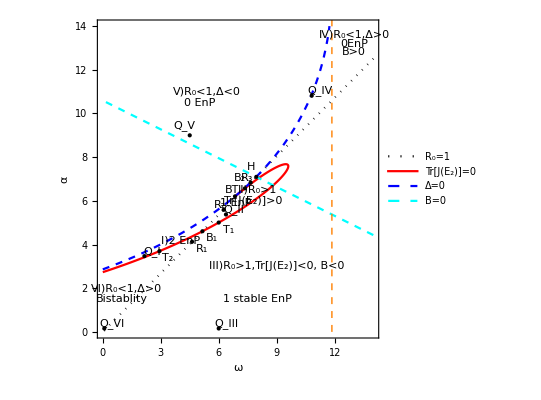

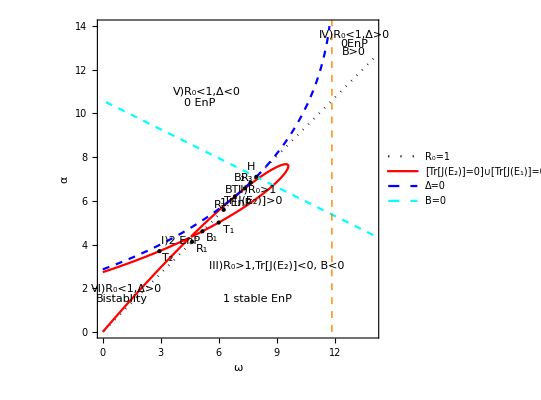

fig6ns.pdf

fig62.pdf

```mathematica
(**Fig 6ns/3, Fig62/4 *)
cn=Param
xm=0;ym=0;xM=14;yM=14;
(*μ/(Subscript[v, 1])//.cn//N*)
p1g=Graphics[{Thick,Orange,Dashed,Line[{{μ/(Subscript[v, 1])//.cn,0},{μ/(Subscript[v, 1])//.cn,45}}]}];
R0ωa=(R0//.cn/.η->α/ω);
disωa=(dis/.ceta//.cn);
Bbωa=(Bb/.ceta//.cn);
trωa=(trE2/.ceta//.cn);
trω2=((rest)/.ceta//.cn);

trω=((trG//.cv1)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},PlotPoints -> 200,  
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
  ptr2=ContourPlot[trω2==0,{ω,xm,xM},{α,ym,yM},PlotPoints -> 290, 
 MaxRecursion -> 2, WorkingPrecision -> 35, ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"[Tr[J(E_2)]=0]∪[Tr[J(E_1)]=0]"}];
 
 
Print["dis at BTP is "]
Chop[Evaluate[disωa//.testBTP//N]]
Print["Dis at H ="]
dis//.testHP//N

pR0=ContourPlot[R0ωa==1,{ω,xm,xM},{α,ym,yM},ContourStyle->{Black,Dotted},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},Frame->True,PlotLegends->{"R_0=1"}];
 
pD=ContourPlot[disωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{ Blue,Dashed}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},
PlotLegends->{"Δ=0"}];

pB=ContourPlot[Bbωa==0,{ω,xm,xM},{α,ym,yM},
ContourStyle->{Dashed,Cyan}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"B=0"}];

 epi= {Black,Style[Text["V)R_0<1,Δ<0",{5.4,11}],13],Style[Text["0 EnP",{5,10.5}],13],
Style[Text["Tr[J(E_2)]>0",{7.8,6}],6],Style[Text["II)R_0>1",{8,6.5}],7],Style
[Text["1 EnP",{6.9,5.9}],6],
Style[Text["IV)R_0<1,Δ>0",{13,13.6}],10],Style[Text["0EnP",{13,13.2}],12],
Style[Text["B>0",{13,12.8}],12],
Style[Text[" VI)R_0<1,Δ>0",{1.2,2}],10],Style[Text["Bistablity",{1,1.5}],10],
Style[Text[" I)2 EnP",{4,4.2}],7],
Style[Text[" III)R_0>1,Tr[J(E_2)]<0, B<0",{9,3}],13],
Style[Text["1 stable EnP",{8,1.5}],13]};

PH=Text["H",Offset[{-5,10},{ω,η ω}//.testHP]];PHp={PointSize[Medium],Style[Point[{ω,η ω}
//.testHP],Yellow]};
PBT=Text["BT",Offset[{-3,6},{ω,α}//.testBTP//N]];PBTp={PointSize[Medium],Style[Point[
{ω,α}//.testBTP//N],Red]};
BP1=Text["B_1",Offset[{10,-7},{ω,α}//.BP[[1]]]];BP1p={PointSize[Medium],Style[Point[
{ω,α}//.BP[[1]]],Green]};
BP2=Text["B_2",Offset[{-5,10},{ω,α}//.BP[[2]]]];BP2p={PointSize[Medium],Style[Point[
{ω,α}//.BP[[2]]],Blue]};
P1=Text["R_1",Offset[{10,-7},{ω,α}//.testR1]];P1p={PointSize[Medium],Style[Point[
{ω,α}//.testR1],Purple]};
(*P4=Text["R_4",Offset[{10,-7},{ω,α}//.testR4]];P4p={PointSize[Medium],
Style[Point[{ω,α}//.testR4],Purple]};*)
P3=Text["R_3",Offset[{-4,5},({ω,α}//.testR3)]];
P3p={PointSize[Medium],Style[Point[{ω,α}//.testR3],Purple]};
P2=Text["R_2",Offset[{-4,5},{ω,α}//.testR2]];
P2p={PointSize[Medium],Style[Point[{ω,α}//.testR2],Purple]};
QI=Text["Q_I",Offset[{8,5},{ω,α}//.test[RI]]];QIp={PointSize[Medium],Style[Point[
{ω,α}//.test[RI]],Magenta]};
QII=Text["Q_II",Offset[{8,5},{ω,α}//.test[II]]];QIIp={PointSize[Medium],Style[Point[
{ω,α}//.test[II]],Magenta]};
QIII=Text["Q_III",Offset[{8,5},{ω,α}//.test[III]]];QIIIp={PointSize[Medium],Style[Point[
{ω,α}//.test[III]],Magenta]};
QIV=Text["Q_IV",Offset[{8,5},{ω,α}//.test[IV]]];QIVp={PointSize[Medium],Style[Point[
{ω,α}//.test[IV]],Magenta]};
QV=Text["Q_V",Offset[{-5,10},{ω,α}//.test[V]]];QVp={PointSize[Medium],Style[Point[
{ω,α}//.test[V]],Magenta]};
QVI=Text["Q_VI",Offset[{8,5},{ω,α}//.test[VI]]];QVIp={PointSize[Medium],
Style[Point[{ω,α}//.test[VI]],Magenta]};
QVIa=Text["Q_VIa",Offset[{8,5},{ω,α}//.test[VIa]]];QVIap={PointSize[Medium],
Style[Point[{ω,α}//.test[VIa]],Magenta]};
T1=Text["T_1",Offset[{10,-7},{ω,α}//.testBoIIandIII]];T1a={PointSize[Medium],
Style[Point[{ω,α}//.testBoIIandIII],Black]};
T2=Text["T_2",Offset[{8,-7},{ω,α}//.testBoIandVIa]];T2a={PointSize[Medium],
Style[Point[{ω,α}//.testBoIandVIa],Black]};
regions={RI,II,III,IV,V,VI};
pt=Table[{ω,α}//.test[j],{j,regions}];
pG=Table[Text[P[j],Offset[{-5,10},pt[[j]]]],{j,6}];

epiP={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,P2,P2p,(*P4,P4p,*)QI,QIp,QII,
QIIp,QIII,QIIIp,QIV,QIVp,QV,QVp,QVI,QVIp,T1,T1a,T2,T2a}//N;
epiP1={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,P2,P2p,T1,T1a,T2,T2a}//N;
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epi,epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
fig62=Show[{pR0,ptr2,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epi,epiP1},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]

Export["fig6ns.pdf",fig6F]
Export["fig62.pdf",fig62]
```

#### Blow-up of the Map:

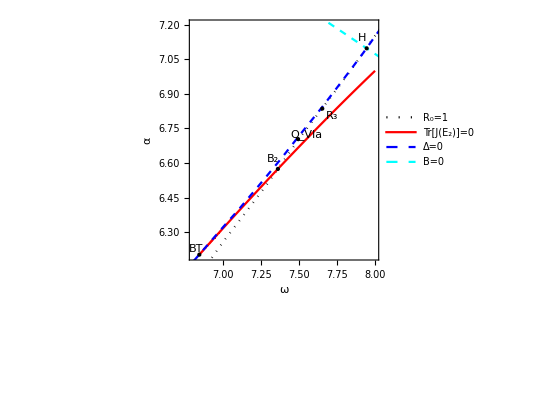

fig6BT.pdf

```mathematica
(*xm=6.8;ym=6.25;xM=7.8;yM=6.9;*)
xm=6.8;ym=6.2;xM=8;yM=7.2;
trωa=((trE2//.cv1)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},PlotPoints -> 200,
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 P3=Text["R_3",Offset[{10,-7},{ω,α}//.testR3]];
 P3p={PointSize[Medium],Style[Point[{ω,α}//.testR3],Purple]};
 epiP1={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p,P1,P1p,P3,P3p,QVIa,QVIap}//N;
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epiP1},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6BT.pdf",fig6F]
```

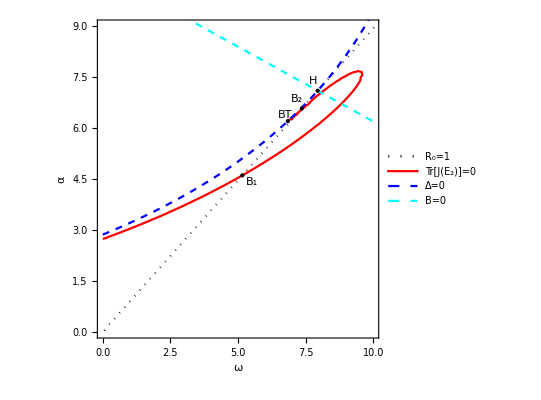

fig6n.pdf

```mathematica
(*xm=6.8;ym=6.25;xM=7.8;yM=6.9;*)
xm=0;ym=0;xM=10;yM=9;
epiP={PH,PHp,PBT,PBTp,BP1,BP1p,BP2,BP2p}//N;
trωa=((trE2//.cv1)/.ceta//.cn);
ptr=ContourPlot[trωa==0,{ω,xm,xM},{α,ym,yM},ContourStyle->{Red},
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"}];
 
fig6F=Show[{pR0,ptr,pD,pB,p1g},PlotStyle->Join[ColorData[97,"ColorList"]],Filling->{3->{0,Yellow}}
,Epilog->{epiP},FrameLabel->{ω,"α"},
PlotRange->{{xm,xM},{ym,yM}}]
Export["fig6n.pdf",fig6F]
```

```mathematica
FindInstance[Join[{R0<1&&dis>0&&Bb>0&&trE2>0},cp,{η==α/ω}]//.Param,{ω,α,η}]//N
Solve[Join[{η==η0&&Bb==0&&trE2>0},cp,{η==α/ω}]//.Param,{ω,α,η}]
```

{}

```mathematica
(*At the boundary tr(E2)=0 between I and VIa**)
FindInstance[Join[{trE2==0&& dis>0 && R0ωa<1},Drop[cp,{7,9}],{η0>0}]/.ceta//.Param,{ω,α},6][[6]]
```

{ω→251/71,α→Root3.93Root[-139002992484639814900593+78478625880764526752550 #1-11766747132421728060625 #1^2+202603249788006375000 #1^3&,2]3.9255178935033967}

```mathematica
ωBTP=ω/.testBTP;
ωBP=ω/.testBP;
aBTP=α/.testBTP;
aBP=α/.testBP;
BR01=FindInstance[Join[{α==ω η0, ωBP<ω<ωBTP ,aBP <α<aBTP},Drop[cp,{7,9}],{η0>0}]//.Param,{ω,α},50];
Drop[BR01,30];
Print["Points betωeen BP and BTP "]
Drop[BR01,30]//N
Print["Points betωeen 0 and BP "]
BR01a=FindInstance[Join[{α==ω η0, 0<ω<ωBP ,0<α<aBP},Drop[cp,{7,9}],{η0>0}]//.Param,{ω,α},10];
BR01a
BR01a//N
Print["α and ω at BTP and boundary R0==1 are respectively "]
alBTP= ω η0//.testBTP//N
ω//.BTP//N
Print["α and ω at BP are respectively "]
alBP= ω η0//.testBP//N
ω//.BP//N

R0//.testBP//N

FindInstance[Join[{α==ω η0, (ω/.BR[[2]])<ω<(ω/.HP) ,(α/.BR[[2]]) <α<(α/.HP)},Drop[cp,{7,9}],{η0>0}]//.Param,{ω,α},6]
%//N
```

Points betωeen BP and BTP

{{ω→6.18693,α→5.52699},{ω→6.18963,α→5.5294},{ω→6.20209,α→5.54053},{ω→6.21421,α→5.55136},{ω→6.23779,α→5.57243},{ω→6.27989,α→5.61004},{ω→6.28697,α→5.61636},{ω→6.30145,α→5.62929},{ω→6.30549,α→5.6329},{ω→6.32031,α→5.64614},{ω→6.48535,α→5.79358},{ω→6.57494,α→5.87361},{ω→6.58774,α→5.88505},{ω→6.6029,α→5.89859},{ω→6.61165,α→5.90641},{ω→6.65005,α→5.94071},{ω→6.69586,α→5.98163},{ω→6.71708,α→6.00059},{ω→6.76625,α→6.04452},{ω→6.79993,α→6.07461}}

Points betωeen 0 and BP

{{ω→46/195,α→3082/14625},{ω→16/65,α→1072/4875},{ω→27/65,α→603/1625},{ω→89/39,α→5963/2925},{ω→178/65,α→11926/4875},{ω→574/195,α→38458/14625},{ω→709/195,α→47503/14625},{ω→713/195,α→47771/14625},{ω→901/195,α→60367/14625},{ω→190/39,α→2546/585}}

{{ω→0.235897,α→0.210735},{ω→0.246154,α→0.219897},{ω→0.415385,α→0.371077},{ω→2.28205,α→2.03863},{ω→2.73846,α→2.44636},{ω→2.94359,α→2.62961},{ω→3.6359,α→3.24807},{ω→3.65641,α→3.26639},{ω→4.62051,α→4.12766},{ω→4.87179,α→4.35214}}

α and ω at BTP and boundary R0==1 are respectively

6.11203

6.84183

α and ω at BP are respectively

4.60724

{5.15735,7.35966}

1.

{{ω→7611/1028,α→169979/25700},{ω→7715/1028,α→103381/15420},{ω→1943/257,α→130181/19275},{ω→2027/257,α→135809/19275},{ω→8139/1028,α→181771/25700},{ω→8153/1028,α→546251/77100}}

{{ω→7.4037,α→6.61397},{ω→7.50486,α→6.70435},{ω→7.56031,α→6.75388},{ω→7.88716,α→7.04586},{ω→7.91732,α→7.0728},{ω→7.93093,α→7.08497}}

{α→(3 ω)/5}

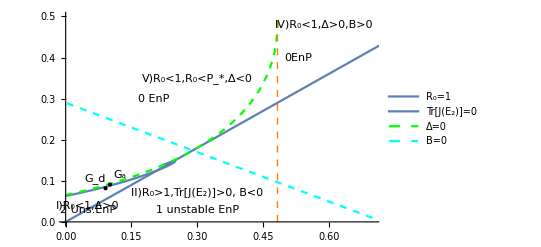

```mathematica
(**Fig Gupta*)
paramGG=Thread[{Λ,δ,γ,β,ξ,μ,Subscript[v, 2],Subscript[v, 1]}->{1/2,2/10,1/10,2/10,7/100,1/10,(μ+γ+δ),(β+ μ ξ)}];
cn=paramGG;
xM=.7;La=.5;
p1g=Graphics[{Thick,Orange,Dashed,Line[{{μ/(Subscript[v, 1])//.cn,0},{μ/(Subscript[v, 1])//.cn,La}}]}];
R0ωa=(R0/.cV2//.cn/.η->α/ω);
aω=Solve[R0ωa==1,α][[1]]
pR0=Plot[α/.aω,{ω,0,20},PlotLegends->{"R_0=1"},LabelStyle->{Black,Bold}];
 disωa=(dis/.ceta//.cn);
pD=ContourPlot[disωa==0,{ω,0,xM},{α,0,La},
ContourStyle->{Thick, Dashed,Green}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},
PlotLegends->{"Δ=0"}];
Bbωa=(Bb/.ceta//.cn);
pB=ContourPlot[Bbωa==0,{ω,0,xM},{α,0,La},
ContourStyle->{Dashed,Cyan}, AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"B=0"}];
trωa=((trE2//.cv1)/.ceta//.cn);
pTr=ContourPlot[trωa==0,{ω,0,xM},{α,0,La},ContourStyle->Broωn,
 AxesLabel->{ω,"α"},LabelStyle->{Black,Bold},PlotLegends->{"Tr[J(E_2)]=0"},MaxRecursion->5];
epi= {Black,Style[Text["V)R_0<1,R_0<P_*,Δ<0",{0.3,0.35}],13],Style[Text["0 EnP",{0.2,0.3}],13],
Style[Text["Tr[J(E_2)]<0",{11.3,10.5}],12],Style[Text["III)R_0>1,1 EnP",{13,12}],12],
Style[Text["IV)R_0<1,Δ>0,B>0",{0.59,0.48}],10],Style[Text["0EnP",{0.53,0.4}],12],

Style[Text[" I)R_0<1,Δ>0",{0.05,0.04}],6],Style[Text["2 Uns.EnP",{0.05,0.03}],7],
Style[Text[" VI)Bistability",{3,4.7}],6],
Style[Text[" II)R_0>1,Tr[J(E_2)]>0, B<0",{0.3,0.07}],11],
Style[Text["1 unstable EnP",{0.3,0.03}],11]};
Gca1=Text["G_a",Offset[{10,10},{ω,α}//.ParGca]];GcaS1={PointSize[Medium],Style[Point[{ω,α}//.ParGca],Cyan]};
Gcd1=Text["G_d",Offset[{-10,10},{ω,α}//.ParGcd]];GcdS1={PointSize[Medium],Style[Point[{ω,α}//.ParGcd],Blue]};
epiG={Gca1,GcaS1,Gcd1,GcdS1};
mapG=Show[{pR0,pTr,pD,pB,p1g},Epilog->{epi,epiG},FrameLabel->{ω,"α"},
PlotRange->{{0,xM},{0,La}}]
```

#### Bifurcation diagram :

{Λ→16,δ→1/5,γ→3/25,ξ→1/1000,μ→3/25,v_2→γ+δ+μ,v_1→β+μ ξ,V_2→γ+δ+η+μ,ω→5/64,α→5/32}

β*=0.0183 ,β_(1*)=0.00271739 ,β_(2*)=0.0040654

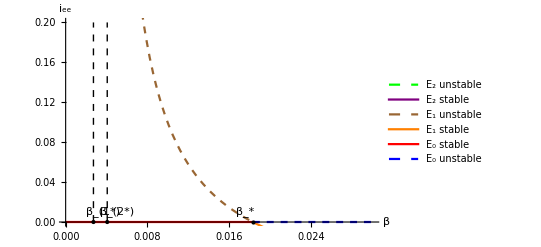

```mathematica
(**Bifurcation Diagram of Region VI*)
cn=Drop[test[VI],{4}]
xm=0;ym=0;xM=3/100;yM=2/10;

dis0=β/.Solve[dis==0,β];

Print["β*=",b0n= b0/.cV2/.cv2/.η->α/ω//.cn//N, " ,β_(1*)=", bc1=dis0[[1]]/.η->α/ω//.cn//N, " ,β_(2*)=", bc2=dis0[[2]]/.η->α/ω//.cn//N]

lin1=Line[{{ bc1,0},{ bc1,yM}}];
li1=Graphics[{Thick,Black,Dashed,lin1}];
lin2=Line[{{ bc2,0},{ bc2,yM}}];
li2=Graphics[{Thick,Black,Dashed,lin2}];
pE2a=Plot[{ie[[2]]/.η->α/ω}//.cn,{β,0,b0n},PlotStyle->{Dashed,Thick,Green},PlotRange->All,PlotLegends->{"E_2 unstable"}];
pE2b=Plot[{ie[[2]]/.η->α/ω}//.cn,{β,b0n,xM},PlotStyle->{Thick,Purple},
PlotRange->All,PlotLegends->{"E_2 stable"}];
pE1a=Plot[{ie[[1]]/.η->α/ω}//.cn,{β,0,b0n},PlotStyle->{Dashed,Thick,Brown},PlotRange->All,PlotLegends->{"E_1 unstable"}];
pE1b=Plot[{ie[[1]]/.η->α/ω}//.cn,{β,b0n,xM},PlotStyle->{Thick,Orange},
PlotRange->All,PlotLegends->{"E_1 stable"}];
pdfea=Plot[0,{β,0, b0n},PlotStyle->{Thick,Red},PlotRange->All,
PlotLegends->{"E_0 stable"}];
pdfeb=Plot[0,{β,b0n, xM},PlotStyle->{Dashed,Thick,Blue},PlotRange->All,
PlotLegends->{"E_0 unstable"}];
bifNO=Show[{pE2a, pE2b,pE1a, pE1b,pdfea,pdfeb,li1,li2},PlotRange->{{0,xM},{0,yM}},Epilog->
{{Text["β_*",Offset[{-8,10},{ b0n,0}]],{PointSize[Large],
Style[Point[{ b0n,0}],Orange]},Text["β_(2*)",Offset[{10,10},{ bc2,0}]],
{PointSize[Large],Style[Point[{ bc2,0}],Yellow]},Text["β_(1*)",Offset[{10,10},{ bc1,0}]],
{PointSize[Large],Style[Point[{ bc1,0}],Black]}}
},AxesLabel->{"β","i_ee"}]
```